# Energy Levels and Spectrum

## No Selection Rules

```mathematica
(* Energy Levels *)
EnergyLevel[n_]:=Join[{0},Sort[ Table[RandomReal[{0,10}],{i,1,n-1}],#1<#2&]]
(* EngPlot *)
EngPlot[lis_]:=ListPlot[lis,Filling -> Axis,PlotRange-> {0,10}]
(* Display List *)
DisList[lis_]:=TableForm[Table[If[lis[[j]]-lis[[i]]> 0,lis[[j]]-lis[[i]],"---"],{i,1,Length[lis]},{j,1,Length[lis]}],TableHeadings->{lis,lis}]
(* Generate Spectrum *)
Spectrum[lis_]:=Sort[Flatten[Table[lis[[j]]-lis[[i]],{i,1,Length[lis]-1},{j,i+1,Length[lis]}]],#1<#2&]
(* Plot Spectrum *)
SpecPlot[lis_]:=ListPlot[Table[{lis[[i]],1},{i,1,Length[lis]}],Filling -> Axis,PlotRange->{{0,All},{0,1}},AspectRatio->0.3]
```

| 0 | 3.69936 | 4.60967 | 8.97039 | 9.51437
0 | --- | 3.69936 | 4.60967 | 8.97039 | 9.51437
3.69936 | --- | --- | 0.910311 | 5.27104 | 5.81502
4.60967 | --- | --- | --- | 4.36072 | 4.9047
8.97039 | --- | --- | --- | --- | 0.543981
9.51437 | --- | --- | --- | --- | ---

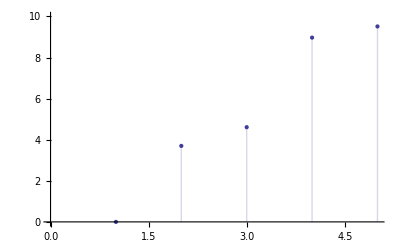

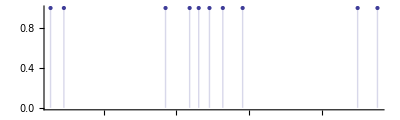

{0.543981,0.910311,3.69936,4.36072,4.60967,4.9047,5.27104,5.81502,8.97039,9.51437}

```mathematica
g=EnergyLevel[5];
gS=Spectrum[g];
DisList[g]
EngPlot[g]
SpecPlot[gS]
gS
```

### Reconstructure

```mathematica
SumList[S_]:=Flatten[DeleteCases[DeleteCases[Table[If[S[[i]]+S[[j]]==S[[k]],{i,j,k},0],{i,1,Length[S]},{j,i+1,Length[S]},{k,1,Length[S]}],0,{3}],{},2],2]
```

```mathematica
ReCon[S_]:=Module[{gD,gRow,gdump},
gD=Table[Count[SumList[S],{_,_,i}],{i,1,Length[S]}];
gRow=Table[DeleteCases[Table[If[gD[[i]]==n,S[[i]],0],{i,1,Length[gD]}],0],{n,0,Max[gD]}];
gdump=DeleteCases[Table[If[gRow[[-2,1]]+gRow[[-2,2]]-gRow[[-1,1]]==S[[i]],S[[i]],0],{i,1,Length[S]}],0][[1]];
{
{gRow[[-1,1]],gRow[[-2,1]],DeleteCases[Table[If[gRow[[-2,1]]-gdump==S[[i]],S[[i]],0],{i,1,Length[S]}],0][[1]],0},
{gRow[[-1,1]],gRow[[-2,2]],DeleteCases[Table[If[gRow[[-2,2]]-gdump==S[[i]],S[[i]],0],{i,1,Length[S]}],0][[1]],0}
}
]
```

```mathematica
t=g
tS=Permutations[Spectrum[g]][[500]]
tD=Table[Count[SumList[tS],{_,_,i}],{i,1,Length[tS]}];
TableForm[Join[{tS},{tD}],TableDirections->Row]
tLevel=Table[DeleteCases[Table[If[tD[[i]]==n,tS[[i]],0],{i,1,Length[tD]}],0],{n,Max[tD],0,-1}];
tLevel//TableForm
```

{0,3.69936,4.60967,8.97039,9.51437}

{0.543981,0.910311,3.69936,4.36072,8.97039,4.60967,9.51437,4.9047,5.81502,5.27104}

0.543981
0.910311
3.69936
4.36072
8.97039
4.60967
9.51437
4.9047
5.81502
5.27104 | 0
0
0
0
2
1
3
1
2
1

9.51437 |  |  | 
8.97039 | 5.81502 |  | 
4.60967 | 4.9047 | 5.27104 | 
0.543981 | 0.910311 | 3.69936 | 4.36072

```mathematica
tG[Levellis_,Spec_,r_,s_]:=If[r≥3 ∧ r-1≥ s≥ 2,
Table[
If[Levellis[[r-1,s-1]]+Levellis[[r-1,s]]-Levellis[[r-2,s-1]]==Spec[[i]],Spec[[i]],0]
,{i,1,Length[tS]}]
,{1}]
```

```mathematica
P=Module[
{q1,qsize},
qsize=Length[tLevel];
q1=Table[0,{i,qsize,1,-1},{j,i,qsize}];
q1[[1]]=tLevel[[1]];
q1[[2]]={tLevel[[2,1]],tLevel[[2,2]]};
q1[[3,2]]=DeleteCases[tG[q1,tS,3,2],0][[1]];
Table[
q1[[3,1]]=Select[tLevel[[3]],#1≠ q1[[3,2]]&][[3/2+(-1)^i 1/2]];
q1[[3,3]]=Select[tLevel[[3]],#1≠ q1[[3,2]]&][[3/2-(-1)^i 1/2]];
If[Count[tG[q1,tS,4,2],0]≠(Length[q1]+1)Length[q1]/2,
q1[[qsize,2]]=DeleteCases[tG[q1,tS,qsize,2],0][[1]];
q1[[qsize,3]]=DeleteCases[tG[q1,tS,qsize,3],0][[1]];
q1[[qsize,1]]=DeleteCases[Table[If[q1[[3,1]]-q1[[qsize,2]]==tS[[i]],tS[[i]],0],{i,1,Length[tS]}],0][[1]];
q1[[4,4]]=DeleteCases[Table[If[q1[[3,3]]-q1[[4,3]]==tS[[i]],tS[[i]],0],{i,1,Length[tS]}],0][[1]];
q1,
0],{i,1,2}]
];
P[[1]]//TableForm
```

9.51437 |  |  | 
8.97039 | 5.81502 |  | 
4.60967 | 5.27104 | 4.9047 | 
3.69936 | 0.910311 | 4.36072 | 0.543981